## Kinematics

```mathematica
SetDirectory[NotebookDirectory[]]
Get["EVA_luminosity.m"];
MetricM={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
```

/Users/ishmammahbub/Desktop/Research/Partonic Distribution/WWtt/Plot Partonic Distribution

Get::noopen: Cannot open EVA_luminosity.m.

```mathematica
pw=Sqrt[E0^2-mW^2];
pt=Sqrt[E0^2-mt^2];
p10={E0,0,0,pw};p20={E0,0,0,-pw};
k10={E0,pt Sin[θ],0,pt Cos[θ]};
k20={E0,-pt Sin[θ],0,-pt Cos[θ]};
ep10={pw/mW,0,0,E0/mW};ep20={pw/mW,0,0,-E0/mW};
```

```mathematica
SPro[a_,b_]:=a.MetricM.b
```

## Spinor Definition from Reece

```mathematica
uplus[e_, p_, θ_] := {Sqrt[e - p] Cos[θ/2], Sqrt[e-p] Sin[θ/2], Sqrt[e+p] Cos[θ/2], Sqrt[e+p]  Sin[θ/2]};
```

```mathematica
uminus[e_, p_, θ_] := {-Sqrt[e + p ]Sin[θ/2], Sqrt[e+p]Cos[θ/2], -Sqrt[e-p]  Sin[θ/2], Sqrt[e-p] Cos[θ/2]};
```

```mathematica
vplus[e_, p_, θ_] := {-Sqrt[e + p] Sin[θ/2], Sqrt[e+p]Cos[θ/2], Sqrt[e-p]  Sin[θ/2], -Sqrt[e-p] Cos[θ/2]};
```

```mathematica
vminus[e_, p_, θ_] := {-Sqrt[e - p] Cos[θ/2], -Sqrt[e-p]  Sin[θ/2], Sqrt[e+p] Cos[θ/2], Sqrt[e+p]  Sin[θ/2]};
```

```mathematica
IdM={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
γ0 = {{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};
```

```mathematica
γ1 = {{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
```

```mathematica
γ2 = {{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
```

```mathematica
γ3 = {{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};
```

```mathematica
γ5 = {{-1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
PL=(IdM-γ5)/2;
PR=(γ5 +IdM)/2;
```

```mathematica
uplusbar[e_, p_, θ_] := {Sqrt[e - p] Cos[θ/2], Sqrt[e-p] Sin[θ/2], Sqrt[e+p] Cos[θ/2], Sqrt[e+p] Sin[θ/2]}.γ0;
```

```mathematica
uminusbar[e_, p_, θ_] := {-Sqrt[e + p] Sin[θ/2], Sqrt[e+p]Cos[θ/2], -Sqrt[e-p]  Sin[θ/2], Sqrt[e-p] Cos[θ/2]}.γ0;
```

```mathematica
vplusbar[e_, p_, θ_] := {-Sqrt[e + p] Sin[θ/2], Sqrt[e+p]Cos[θ/2], Sqrt[e-p]  Sin[θ/2], -Sqrt[e-p] Cos[θ/2]}.γ0;
```

```mathematica
vminusbar[e_, p_, θ_] := {-Sqrt[e - p] Cos[θ/2], -Sqrt[e-p] Sin[θ/2], Sqrt[e+p] Cos[θ/2], Sqrt[e+p] Sin[θ/2]}.γ0;
```

```mathematica
uminusbar[E0,pt,θ].vminus[E0,pt,-θ]//Simplify
uminusbar[E0,pt,θ].vplus[E0,pt,-θ]//Simplify
uplusbar[E0,pt,θ].vplus[E0,pt,-θ]//Simplify
uplusbar[E0,pt,θ].vminus[E0,pt,-θ]//Simplify
```

-2 √(E0^2-mt^2) Sin[θ]

0

2 √(E0^2-mt^2) Sin[θ]

0

## Amplitude

### Diagram 1

```mathematica
Amp1[ubar_,v_]:=-ee^2/(2 sint^2)mt 1/(SPro[k10+k20,k10+k20]-mh^2)(1+dyt)SPro[ep10,ep20]Dot[ubar,v];
```

### Diagram 2

```mathematica
GaMatrixPro[p_]:=p[[1]]γ0-p[[2]]γ1-p[[3]]γ2-p[[4]]γ3
```

```mathematica
Amp2[ubar_,v_]=(2 ee^2)/3 1/SPro[k10+k20,k10+k20]((SPro[k10,ep20]+SPro[k20,ep20]+SPro[p10,ep20])ubar.GaMatrixPro[ep10].v-(SPro[k10,ep10]+SPro[k20,ep10]+SPro[p20,ep10])ubar.GaMatrixPro[ep20].v+SPro[ep10,ep20]ubar.GaMatrixPro[p20-p10].v)//Simplify;
```

#### Diagram 3

```mathematica
Amp3[ubar_,v_]=-I (ee cost)/sint 1/(SPro[k10+k20,k10+k20]-mZ^2)I ee((SPro[k10,ep20]+SPro[k20,ep20]+SPro[p10,ep20])1/(6 sint cost)(-ubar.(4 sint^2 GaMatrixPro[ep10].PR+(4 sint^2-3)GaMatrixPro[ep10].PL).v)-
(SPro[k10,ep10]+SPro[k20,ep10]+SPro[p20,ep10])1/(6 sint cost)(-ubar.(4 sint^2 GaMatrixPro[ep20].PR+(4 sint^2-3)GaMatrixPro[ep20].PL).v)+(SPro[ep10,ep20])1/(6 sint cost)(ubar.(4 sint^2 GaMatrixPro[p10-p20].PR+(4 sint^2-3)GaMatrixPro[p10-p20].PL).v))//Simplify;
```

#### Diagram 4

```mathematica
Amp4[ubar_,v_]= ee^2/(2 sint^2)1/(SPro[p20-k10,p20-k10](*-mb^2*))ubar.GaMatrixPro[ep20].PL.(GaMatrixPro[k10-p20](*+mb IdM*)).GaMatrixPro[ep10].PL.v//Simplify;
```

## Total Amplitude

```mathematica
AmpTotal[ubar_,v_]:=Amp1[ubar,v]+Amp2[ubar,v]+Amp3[ubar,v]+Amp4[ubar,v];
```

```mathematica
app=AmpTotal[uplusbar[E0,pt,θ],vplus[E0,pt,Pi+θ]]//TrigReduce//Simplify;
apm=AmpTotal[uplusbar[E0,pt,θ],vminus[E0,pt,Pi+θ]]//TrigReduce//Simplify;
amp=AmpTotal[uminusbar[E0,pt,θ],vplus[E0,pt,Pi+θ]]//TrigReduce//Simplify;
amm=AmpTotal[uminusbar[E0,pt,θ],vminus[E0,pt,Pi+θ]]//TrigReduce//Simplify;
```

## Parameter choice

```mathematica
Nc=3;
```

```mathematica
para={mW->80.379,mZ->91.1876,mh->125.,mt->173,sint->0.479,cost->0.878,ee->0.3128};
Msquare=Nc(app^2+apm^2+amp^2+amm^2);
```

## Integrated over the phase space

```mathematica
dsigma=(1/(8 E0 pw)pt/((2Pi)^2 4*2E0)Msquare)//.para;
dsigma0=dsigma//.dyt->0;
```

```mathematica
numerical[energy_] := NIntegrate[2Pi Sin[θ](dsigma0//.{E0->energy}),{θ,0,Pi}];
```

```mathematica
0.3894*10^9*numerical[3000]
```

7.93548

### Scan

```mathematica
sqrtsList=Table[350+25*i,{i,0,400}];
thetaList=Table[0+(Pi/18)*i,{i,0,18}];
sqrtsmu=10000
```

10000

```mathematica
sigSM=Table[NIntegrate[2Pi Sin[θ](dsigma0//.{E0->sqrtsList[[i]]/2}),{θ,0,Pi}],{i,1,Length@sqrtsList}];
```

ColorData::notent: colorselecitonumber is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

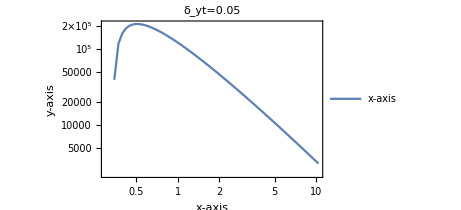

```mathematica
factor=0.3894*10^12;
lineplot=ListLogLogPlot[{Transpose[{sqrtsList/10^3,factor*sigSM}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][5],Dashing[Large]},Frame->True,FrameLabel->{Style["x-axis",Black,13,FontFamily->"Times"],Style["y-axis",Black,13,FontFamily->"Times"]},
PlotLabel->Style["δ_yt=0.05",Black,20],
PlotLegends->Placed[{Style["x-axis",Black,10,FontFamily->"Times"]},{0.8,0.9}],
FrameTicksStyle->Directive[Black,13]]
(*customticks package*)
```

```mathematica
Export["ww00_partonic.dat",sigSM]
```

ww00_partonic.dat